# MATH 022 Lab 10

## Arclength and Surface Area

By Helen P. Read, University of Vermont. Last revised April 2015

Name: Samuel Pakulski

Show your work, and record your answers in the boxes provided. Use NIntegrate for all of the integrals, to the default precision.

To revolve a parametric curve {x[t],y[t]} around the y-axis for t∈[a,b], use 

RevolutionPlot3D[{x[t],y[t]},{t,a,b}]

To revolve around the x-axis, include the option RevolutionAxis→x

## Exercise 1

### (a)

Express the curve given by x=1/3 y sin^2(4y) for  0≤y≤π  parametrically, and use ParametricPlot to plot it. Then answer the following questions.

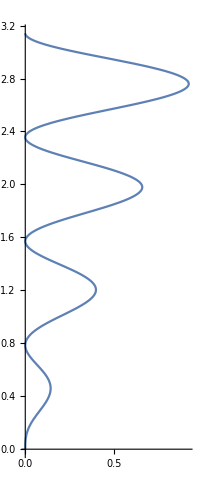

```mathematica
x[t_]:=1/3t*Sin[4t]^2
y[t_]:=t
ParametricPlot[{x[t],y[t]},{t,0,π}]
```

### (b)

```mathematica
NIntegrate[√((x'[t])^2+(y'[t])^2),{t,0,π}]
```

5.64362

Find the length of the curve.

arclength: 5.64362

### (c)

```mathematica
RevolutionPlot3D[{x[t],y[t]},{t,0,π}]
```

-Graphics3D-

```mathematica
NIntegrate[2π(x[t])(√((x'[t])^2+(y'[t])^2)),{t,0,π}]
```

10.9677

Use RevolutionPlot3D to revolve the curve around the y-axis, and find the resulting surface area.

surface area: 10.9677

### (d)

```mathematica
NIntegrate[2π(6-y[t])(√((x'[t])^2+(y'[t])^2)),{t,0,π}]
```

146.845

Find the surface area if the curve is revolved around the line x=6. (You do not need to plot the surface, but do try to visualize it.)

surface area: 146.845

## Exercise 2

### (a)

Plot the following parametric curve for t∈[-10,10]

x=918+12 t-50 t^2-2 t^3
y=2438-154 t+31 t^2+4 t^3-t^4

Then answer the following questions.

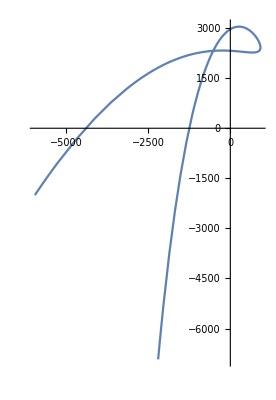

```mathematica
x[t_]:=918+12 t-50 t^2-2 t^3
y[t_]:=2438-154 t+31 t^2+4 t^3-t^4
ParametricPlot[{x[t],y[t]},{t,-10,10}]
```

### (b)

Determine when and where the curve crosses itself. A Manipulate plot may be helpful, but you must show additional work (tables etc.) to support your answer fully.

Location of the point where the curve crosses itself: ("x-coord","y-coord")
Times when the curve goes through the crossing point: t = "smaller value" and t = "larger value"

### (c)

Make a new plot that shows only the loop (in between where the curve intersects itself), and find the length of the loop. Set the AxesOrigin → {0, 0} in your plot.

arclength: "answer"

### (d)

Use RevolutionPlot3D to revolve the loop around the x-axis, and find the resulting surface area.

surface area: "answer"

### (d)

(d) Find the surface area if the loop is revolved around the line y=-4000. (You do not need to plot the surface, but do try to visualize it.)

surface area: "answer"

## Bonus

Make up your own parametric curve(s), and revolve them around the x- or y-axis to make a cool picture. You can combine multiple revolution plots with Show. 

It might help to set PlotRange→Automatic or PlotRange→All, especially if you use Show to combine plots. 

You can take away the numbered axes and the box around the plot with the options Axes → False, Boxed → False.

\[FreakedSmiley] If submitting electronically, delete your output before you quit (otherwise the file will be too large to submit). Click Cell (up on the main menu), Delete All Output, and save your file. You can restore the output at any time by opening up the file and clicking on Evaluate, Evaluate Notebook.